```mathematica
(* load donut.nb first *)
```

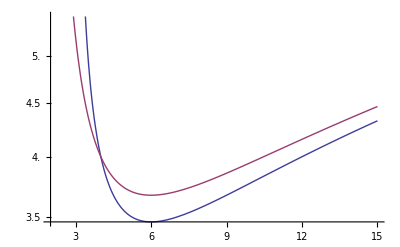

```mathematica
(* Keplerian profiles *)
utK[r_,a_]:=(r^2-2 r+a √r)/(r √(r^2-3r+2a √r))
uphiK[r_,a_]:=(r^2-2 a √r+a^2)/(√r √(r^2-3r+2a √r))
ellK[r_,a_]:=uphiK[r,a]/utK[r,a]
LogPlot[{uphiK[r,0],ellK[r,0]},{r,2,15}]
rmax[ellin_,a_]:=Quiet[NSolve[ellK[r,a]==ellin,r,Reals]][[2,1,2]]
```

```mathematica
α=0.1;
mdot=0.5;
myH=.15myR;
myΣ=1.5 10^4;
myell=7.3657; (* R=50 *)


α=0.1;
mdot=0.5;
myH=.15myR;
myΣ=1. 10^4;
myell=5.868; (* R=30 *)


α=0.1;
mdot=1;
myH=.3myR;
myΣ=1 10^4;
myell=7.3657; (* R=50 *)


α=0.1;
mdot=10;
myH=.5myR;
myΣ=6 10^3;
myell=7.3657; (* R=50 *)


α=0.1;
mdot=100; 
myH=.79myR; (* old: .65 *)
myΣ=12 10^3;
myell=7.3657; (* R=50 *)


α=0.01;
mdot=100;
myH=.79myR;
myΣ=12 10^4;
myell=7.3657; (* R=50 *)


α=0.1;
mdot=100;
myH=.79myR;
myΣ=11 10^3;
myell=5.868; (* R=30 *)

(******)





MBH=10;
a=0;
Rg=MBH 147700;
MdEdd=MBH 2.23 10^18;
Mdot=mdot MdEdd;
myR=rmax[myell,0]
myvr=Mdot/(-2 π myR Rg myΣ)
myUTPOT=Abs[UTPOTatRH[myell,4/3,10^3,a,myR,myH]][[1]]
myKKK=KKKfromsigma[MBH,myell,myUTPOT,4/3,a,myR,myΣ][[1,1,2]]
```

50.0001

-1.60196×10^6

0.99025

23.413

```mathematica
≥
```

```mathematica
donutrhd[MBH,myell,myUTPOT,4/3,myKKK,a,myR,π/2]
```

{1.13917×10^-19,9.5852×10^-25,1.18088×10^-21,1231.98}

```mathematica
≥
```